```mathematica
CS=Sqrt[1-BS];
CE=Sqrt[BE-1];
DS=Sqrt[1-ϕS];
DE=Sqrt[ϕE-1];
vparA=Sqrt[CE^2 vperp^2-DE^2]
vparB=Sqrt[-CS^2 vperp^2+DS^2]
```

√(1+(-1+BE) vperp^2-ϕE)

√(1+(-1+BS) vperp^2-ϕS)

```mathematica
Manipulate[Plot[{√(1+(-1+BE) vperp^2-ϕE),√(1+(-1+BS) vperp^2-ϕS)},{vperp,0,1},AspectRatio->1,AxesLabel->{"v_⊥","v_(||)"},Epilog->{Text["S_1",{0.6,0.6}],Text["S_2",{0.9,0.3}],Text["T",{0.5,0.1}],Text["E_2",{0.2,0.4}]}],{{BE,1.5},1,2},{BS,0,1},{{ϕE,1.04},1,2},{{ϕS,0.5},0,1}]
```

```mathematica
(*{BE->3 10^4 γ,BS->10γ,k->8.617333 10^-5(*eV/K*),e->4.8 10^-10,B->100 γ}*)
```

```mathematica
jUNITS=(e B)/BE NE Sqrt[(k TE)/M];
```

```mathematica
g[Δ_,T_]:=1/BS(Exp[-Δ/(k T)]-(BE-BS)/BE Exp[-Δ/(k T)BE/(BE-BS)]);
jreal=e B(NE Sqrt[(k TE)/(2π m)]g[Δ,TE]-NS Sqrt[(k TS)/(2π m)]Exp[Δ/(k TS)]g[Δ,TS])
```

B e (((ⅇ^(-Δ/(k TE))-((BE-BS) ⅇ^(-(BE Δ)/((BE-BS) k TE)))/BE) NE √((k TE)/m))/(BS √(2 π))-(ⅇ^(Δ/(k TS)) (ⅇ^(-Δ/(k TS))-((BE-BS) ⅇ^(-(BE Δ)/((BE-BS) k TS)))/BE) NS √((k TS)/m))/(BS √(2 π)))

```mathematica
jul=FullSimplify[jreal/jUNITS/.{Δ->x k TE}/.{TS->t TE,NS->n NE,BS->b BE}/.{k->1,TE->1},Assumptions->{x>0,b>0,m>0,M>0,t>0,n>0}]
```

(ⅇ^-x √(M/m) (1+(-1+b) ⅇ^((b x)/(-1+b))-ⅇ^x n √t-(-1+b) ⅇ^(x+(b x)/((-1+b) t)) n √t))/(b √(2 π))

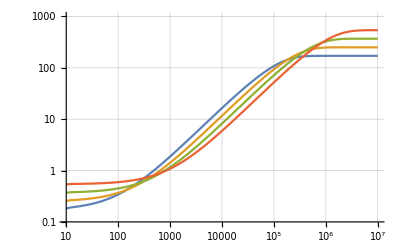

```mathematica
jplot=Expand[-jul/.{b->10^-3,n->10^-3,M-> 1837 m,t->{100,215,465,1000}}];
LogLogPlot[jplot,{x,10^1,10^7},PlotRange->{{10^1,10^7},{10^-1,10^3}},GridLines->Automatic]
```

{-0.0000157379-0.0385371 2.71828^(-1.93473 Δ)+0.0385499 2.71828^(-1.93409 Δ)+0.0000157327 2.71828^(-0.0000386946 Δ),-0.0000497677-0.0385371 2.71828^(-1.93473 Δ)+0.0385499 2.71828^(-1.93409 Δ)+0.0000497511 2.71828^(-3.86946×10^-6 Δ)}

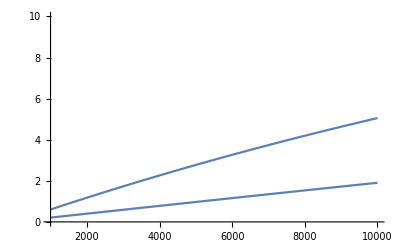

```mathematica
jknight=FullSimplify[jreal/.{
B->2 10^3 γ
,BS->10^1 γ
,BE->3 10^4 γ
,TS->{10^5,10^6}(*K*)
,TE->6000(*K*)
,NS->10^6(*m^-3*)
,NE-> 10^10(*m^-3*)
,k->8.61733 10^-5(*eV K^-1*)
,m->5.10999 10^5/c^2(*eV*)
,e->1.60218 10^-19(*C*)
}/.{
c->2.99792 10^8(*m s^-1*)
}]//N
Quiet[Plot[-jknight 10^6,{Δ,10^3,10^4},PlotRange->{All,{0,10}}]]
```

```mathematica
jreal
```

B e (((ⅇ^(-Δ/(k TE))-((BE-BS) ⅇ^(-(BE Δ)/((BE-BS) k TE)))/BE) NE √((k TE)/m))/(BS √(2 π))-(ⅇ^(Δ/(k TS)) (ⅇ^(-Δ/(k TS))-((BE-BS) ⅇ^(-(BE Δ)/((BE-BS) k TS)))/BE) NS √((k TS)/m))/(BS √(2 π)))